```mathematica
(* This solution uses its own stat mech equations. It does not rely on G16 to compute theromodyanmic functions. It only takes  electronic energies, moments of inertia, and vibrational frequencies from G16 *)
```

```mathematica
(* clear memory *)
ClearAll["Global`*"]
```

```mathematica
(* constants/conversion, SI units unless specified *)
hPlank=6.626070040*10^-34; (* plank constant, SI *)
hbar=hPlank/(2 π);
c0=299792458; (* speed of light, SI *)
kB=1.38064852*10^-23; (* boltzmann constant, SI *)
NA=6.022140857*10^23; (* avogadro's constant, SI *)
Rg=kB*NA; (* gas constant, SI *)

h2j=4.35974 10^-18;(* hartree to joule *)
amu2kg=1.660539040*10^-27; (* atomic mass to kg *)
atm2Pa=101325; (* atm to pascal *)
h2kjmol=2625.499638; (* hartree to kJ/mol *)
h2jmol=2625499.638; (* hartree to J/mol *)
MIau2kgm2=amu2kg*(5.29177×10^-11)^2; (* moment of inertia au to kg.m2 *)
```

```mathematica
Lambda[M_,T_]:=hPlank(2 π M kB T)^(-1/2) ;
Ksi[M_,T_,Energy_]:=(kB T)^-1 (Lambda[M,T])^3 Exp[Abs[Energy](kB T)^-1];
Coverage[M_,T_,Energy_,P_]:=(P Ksi[M,T,Energy])/(1+P Ksi[M,T,Energy]);
```

```mathematica
Energy0=-0.106218423*h2j;
Energy0=-0.028447606*h2j;
Temper0=273.15+4;
Press0=0.124 10^-3 8.314 (273.15+4)/(120 10^-6)
Mass0=32.04*amu2kg;
Energy0*h2kjmol/h2j
Ksi[Mass0,Temper0,Energy0]
Coverage[Mass0,Temper0,Energy0,Press0]
```

2381.03

-74.6892

198.163

0.999998

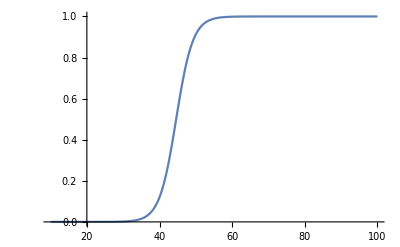

```mathematica
Plot[Coverage[Mass0,Temper0,Ekjmol*h2j/h2kjmol,Press0],{Ekjmol,10,100}]
```

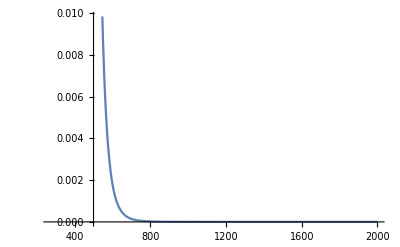

```mathematica
Plot[Coverage[Mass0,Tempr,Energy0,Press0],{Tempr,273,2000}]
```

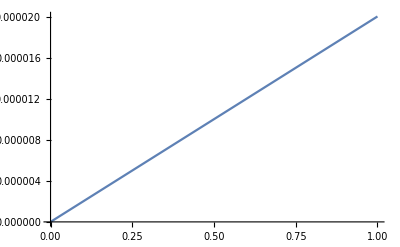

```mathematica
Plot[Coverage[Mass0,Temper0,Energy0,PressAtm*atm2Pa],{PressAtm,10^-26,10^-12}]
```

```mathematica
(* MAIN EQUATIONS, SI units *)


(* q translational *)
Qtran[M_,T_,P_]:=((kB T)/P)((2 π M kB T)/hPlank^2)^(3/2) ;

(* q rotational *)
Qrot[MI_,T_,sig_]:=Sqrt[Pi]/sig((8 π^2 kB T)/hPlank^2)^(3/2)Sqrt[Apply[Times,MI]];
QrotLin[MI_,T_,sig_]:=1/sig((8 π^2 kB T)/hPlank^2)Sqrt[Apply[Times,MI]];

(* q vibrational, freq must be in sec^(-1) *)
Qvib[freq_,T_]:=Apply[Times,Exp[-(freq hPlank)/(2kB T)]]/Apply[Times,1-Exp[-(freq hPlank)/(kB T)]];

(* q electronic, make sure that energies of molecules refer to the same zero level. normally this means that the same method and basis sets are used *)
Qelec[Egs_,Wgs_,T_]:=Wgs Exp[-Egs/(kB T)];

(* Internal energy *)
VibE[x_,T_]=hPlank(x/2+x/(Exp[hPlank x/(kB T)]-1));
TranE[T_]=kB T 3/2;
RotE[T_]=kB T 3/2;
RotELin[T_]=kB T;

(* Many-atom molecule *)
En[freq_,Egs_,T_]:=Egs+RotE[T]+TranE[T]+ Total[VibE[#,T]&/@freq];
EnLin[freq_,Egs_,T_]:=Egs+RotELin[T]+TranE[T]+ Total[VibE[#,T]&/@freq];
(* Single atom/ion does not have rotations and vibrations *)
EnAtom[Egs_,T_]:=Egs+TranE[T];
(* Rigid molecule has translations and rotations but no vibrations *)
EnRigid[Egs_,T_]:=Egs+RotE[T]+TranE[T];
(* Locked system has ONLY electronic DOFs *)
EnLocked[Egs_]:=Egs;

(* Enthalpy *)
H[freq_,Egs_,T_]:=En[freq,Egs,T]+kB T
HLin[freq_,Egs_,T_]:=EnLin[freq,Egs,T]+kB T
HAtom[Egs_,T_]:=EnAtom[Egs,T]+kB T
HRigid[Egs_,T_]:=EnRigid[Egs,T]+kB T
HLocked[Egs_,T_]:=EnLocked[Egs]+kB T

(* Helmholtz free energy *)
A[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs]+Log[Qrot[MI,T,sig]]+Log[Qvib[freq,T]])+Egs
ALin[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs]+Log[QrotLin[MI,T,sig]]+Log[Qvib[freq,T]])+Egs
AAtom[M_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs])+Egs
ARigid[M_,MI_,sig_,Egs_,Wgs_,T_,P_]:=-kB T (Log[ⅇ ]+Log[Qtran[M,T,P]]+Log[Wgs]+Log[Qrot[MI,T,sig]])+Egs
ALocked[Egs_,Wgs_,T_]:=-kB T Log[Wgs]+Egs


(* Gibbs free energy *)
G[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=A[M,MI,sig,freq,Egs,Wgs,T,P]+kB T
GLin[M_,MI_,sig_,freq_,Egs_,Wgs_,T_,P_]:=ALin[M,MI,sig,freq,Egs,Wgs,T,P]+kB T
GAtom[M_,Egs_,Wgs_,T_,P_]:=AAtom[M,Egs,Wgs,T,P]+kB T
GRigid[M_,MI_,sig_,Egs_,Wgs_,T_,P_]:=ARigid[M,MI,sig,Egs,Wgs,T,P]+kB T
GLocked[Egs_,Wgs_,T_]:=ALocked[Egs,Wgs,T]+kB T
```

```mathematica
(* Molecular characteristic, can be found in G16 output files *)

Print["Molecule A = CH3OH"];
MA =32.02621*amu2kg; (* molecular mass *)
MIA={14.25214,74.36048, 77.05765}*MIau2kgm2; (* moments of inertia *)
(* to extract frequencies use bash: 

awk '/Frequencies/{printf("%.4f,%.4f,%.4f,",$3,$4,$5)}' filename.log

*)
SigmaA=1; (* rotational symmetry *)
ElectronicA=-24.0809631117505*h2j; (* electronic energy *)


Print["Molecule B = H2O"];
MB =18.01056*amu2kg;
MIB={2.26960,4.21802,6.48761}*MIau2kgm2;
SigmaB=2;
ElectronicB=-17.2195219555658*h2j;


Print["Surface C = GaN..disA"];
ElectronicC=-8480.62768540887*h2j;


Print["Surface 1 = C..A"];
Electronic1=-8504.73825609188*h2j;

Print["Surface 2"];
Electronic2=-8504.75458912091*h2j;


Print["Surface 3"];
Electronic3=-8504.82453776623*h2j;

Print["Surface 4"];
Electronic4=-8504.84848926423*h2j;

Print["Surface 5"];
Electronic5=-8487.51595729617*h2j;
```

Molecule A = CH3OH

Molecule B = H2O

Surface C = GaN..disA

Surface 1 = C..A

Surface 2

Surface 3

Surface 4

Surface 5

```mathematica
KeqT={};
KrateT={};
Do[
Do[

(* Concetration (mol/L) is specified in the loop
(* convert concetration from mol/L into SI units m^-3 *)
Csi=C0*NA*10^3;
(* compute pressure SI units *)
P0=Csi kB T0;
*)

(* Pressure (Pascal) is specified in the loop *)
(* compute concentration SI units *)
Csi=P0/(kB T0);
(* convert concetration from SI units m^-3 to mol/L *)
C0=Csi/NA*10^-3;

(* the rest is fine *)

V0 =(kB T0)/P0;

Print[];
Print["===================="];
Style[Print["Temperature and concentration = ",T0," Kelvin, ",C0," mol/L"],Red];
Print["Ideal-gas pressure = ",P0/atm2Pa," atm"];
Print["Volume per 1 molecule in SI units = ",V0];


Print["Molecule A"];
(* calculate thermodynamic funtions at 400 K and 2 atm *)
QA=Qtran[MA,T0,P0]Qrot[MIA,T0,SigmaA];
(* evaluate electronic partition function separately, note that this is a gigantic number, cannot be computed in G16 *)
Print["Correct electronic partition function = ",Qelec[ElectronicA,1,T0] ];
(* Gibbs free energy *)
GA=GRigid[MA,MIA,SigmaA,ElectronicA,1,T0,P0];
(* Helmholtz free energy *)
AA=ARigid[MA,MIA,SigmaA,ElectronicA,1,T0,P0];
(* Internal energy *)
EA=EnRigid[ElectronicA,T0];
(* Enthalpy *)
HA=HRigid[ElectronicA,T0];


Print["Molecule B"];
QB =Qtran[MB ,T0,P0]Qrot[MIB ,T0,SigmaB];
Print["Correct electronic partition function = ",Qelec[ElectronicB ,1,T0] ];
GB=GRigid[MB,MIB,SigmaB,ElectronicB ,1,T0,P0];
AB =ARigid[MB ,MIB ,SigmaB  ,ElectronicB,1,T0,P0];
EB =EnRigid[ElectronicB ,T0];
HB =HRigid[ElectronicB ,T0];



Print["Surface C"];
GC =GLocked[ElectronicC ,1,T0];
AC =ALocked[ElectronicC ,1,T0];


Print["Surface 1"];
G1 =GLocked[Electronic1,1,T0];
A1 =ALocked[Electronic1,1,T0];


Print["Surface 2"];
G2 =GLocked[Electronic2,1,T0];
A2 =ALocked[Electronic2,1,T0];


Print["Surface 3"];
G3 =GLocked[Electronic3,1,T0];
A3 =ALocked[Electronic3,1,T0];


Print["Surface 4"];
G4 =GLocked[Electronic4,1,T0];
A4 =ALocked[Electronic4,1,T0];


Print["Surface 5"];
G5 =GLocked[Electronic5,1,T0];
A5 =ALocked[Electronic5,1,T0];





(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 1, path 1 (R1P1): A + C <-> 1"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(Electronic1-ElectronicA - ElectronicC)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(G1-GA-GC)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(A1-AA-AC)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

Neq1 = 1/QA Exp[-DeltaEelectronic/(NA kB T0)];
Print["T- and p-dependent number constant = ",Neq1];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR1P1 =1/(QA/V0 )Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR1P1," m^3 or ",KeqR1P1*10^3*NA," L * mol^-1"];


(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 2, path 1 (R2P1): 1 <-> 2"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(Electronic2-Electronic1)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(G2-G1)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(A2-A1)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR2P1 =Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR2P1];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 3, path 1 (R3P1): 2 <-> 3"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(Electronic3-Electronic2)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(G3-G2)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(A3-A2)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR3P1 =Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR3P1];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 4, path 1 (R4P1): 3 <-> 4"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(Electronic4-Electronic3)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(G4-G3)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(A4-A3)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR4P1 =Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR4P1];



(* Thermodynamic descriptors of the reaction *)

Print[];
Print["Reaction 5, path 1 (R5P1): 4 <-> 5 + B"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(Electronic5+ElectronicB-Electronic4)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GB+G5-G4)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(AB+A5-A4)*NA;

Print["Energy units are J/mol."];Print["Delta E(elec) = ",DeltaEelectronic];
Print["Delta A = ",DeltaA];
Print["Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Delta S = ",(DeltaH-DeltaG)/T0];

(* use partition functions to compute the P-indendent equilibrium costant *)
KeqR5P1 =QB/V0 Exp[-DeltaEelectronic/(NA kB T0)];

Print["Use partition functions. Equilibrium constant = ",KeqR5P1," m^-3 or ",KeqR5P1/(10^3*NA)," mol * L^-1"];



(* Rate constant *)

(*Print[];
Print["Transition state for Reaction 4, path 1 (R4P1): AH..BH..A <-> AAHH..B"];

(* The electronic energy, J/mol *)
DeltaEelectronic=(ElectronicTSAHdotBHdotA-ElectronicAHdotBHdotA)*NA;
(* Internal E, J/mol *)
DeltaE=(ETSAHdotBHdotA-EAHdotBHdotA)*NA;
(* Enthalpy change *)
DeltaH=(HTSAHdotBHdotA-HAHdotBHdotA)*NA;
(* Gibbs FE, J/mol *)
DeltaG=(GTSAHdotBHdotA-GAHdotBHdotA)*NA;
(* Helmholtz FE, J/mol *)
DeltaA=(ATSAHdotBHdotA-AAHdotBHdotA)*NA;

Print["Energy units are J/mol."];Print["Act. Delta E(elec) = ",DeltaEelectronic];
Print["Act. Delta E(intr) = ",DeltaE];
Print["Act. Delta H = ",DeltaH];
Print["Act. Delta A = ",DeltaA];
Print["Act. Delta G = ",DeltaG];
Print["Entropy units are J/mol/K."];
Print["Act. Delta S = ",(DeltaH-DeltaG)/T0];

KrateR4P1 =(kB T0)/hPlank Exp[-(ElectronicTSAHdotBHdotA-ElectronicAHdotBHdotA)/(kB T0)]((QTSAHdotBHdotA/V0)/(QAHdotBHdotA/V0));
Print["Use partition functions. Rate constant = ",KrateR4P1," s^(-1)"];
KrateR4P1 =(kB T0)/hPlank Exp[-(GTSAHdotBHdotA-GAHdotBHdotA)/(kB T0)];
Print["Use activation free energy. Rate constant = ",KrateR4P1," s^(-1)"];

(* save current temperature data into a list: 1/RT vs. Log K_rate *)
KrateT=Append[KrateT,    {1/(kB NA T0),Log[KrateR4P1]}    ];

*)


Print[];
Print["Done with temperature/pressure/concentration: ",T0, ", ", P0, ", ",C0];
Print["===================="];

,{T0,273.15+4,273.15+4,10}]
,{P0,2381,2381,1*atm2Pa}]
 (* Temperature (Kelvin) and pressure (atm) *)(* Temperature (Kelvin) and concetration (mol/L) *)
```

====================

Temperature and concentration = 277.15 Kelvin, 0.00103326 mol/L

Ideal-gas pressure = 2381/101325 atm

Volume per 1 molecule in SI units = 1.60708×10^-24

Molecule A

Correct electronic partition function = 5.3993660416×10^11915

Molecule B

Correct electronic partition function = 3.6043677403×10^8520

Surface C

Surface 1

Surface 2

Surface 3

Surface 4

Surface 5

Reaction 1, path 1 (R1P1): A + C <-> 1

Energy units are J/mol.

Delta E(elec) = -77734.6

Delta A = -12476.8

Delta G = -14781.1

Entropy units are J/mol/K.

Delta S = 0.00360815 (14781.1+DeltaH)

T- and p-dependent number constant = 610.595

Use partition functions. Equilibrium constant = 9.81277×10^-22 m^3 or 590939. L * mol^-1

Reaction 2, path 1 (R2P1): 1 <-> 2

Energy units are J/mol.

Delta E(elec) = -42882.3

Delta A = -42882.3

Delta G = -42882.3

Entropy units are J/mol/K.

Delta S = 0.00360815 (42882.3+DeltaH)

Use partition functions. Equilibrium constant = 1.20754×10^8

Reaction 3, path 1 (R3P1): 2 <-> 3

Energy units are J/mol.

Delta E(elec) = -183650.

Delta A = -183650.

Delta G = -183650.

Entropy units are J/mol/K.

Delta S = 0.00360815 (183650.+DeltaH)

Use partition functions. Equilibrium constant = 4.09223×10^34

Reaction 4, path 1 (R4P1): 3 <-> 4

Energy units are J/mol.

Delta E(elec) = -62884.6

Delta A = -62884.6

Delta G = -62884.6

Entropy units are J/mol/K.

Delta S = 0.00360815 (62884.6+DeltaH)

Use partition functions. Equilibrium constant = 7.10674×10^11

Reaction 5, path 1 (R5P1): 4 <-> 5 + B

Energy units are J/mol.

Delta E(elec) = 296707.

Delta A = 243311.

Delta G = 245615.

Entropy units are J/mol/K.

Delta S = 0.00360815 (-245615.+DeltaH)

Use partition functions. Equilibrium constant = 3.18861×10^-23 m^-3 or 5.29481×10^-50 mol * L^-1

Done with temperature/pressure/concentration: 277.15, 2381, 0.00103326

====================

```mathematica
SolutionR1P1=Solve[Cx/(C0-Cx)^2==KeqR1P1*(10^3*NA),Cx]
SolutionR1P2=Solve[Cx/(C0-Cx)^3==KeqR1P2*(10^3*NA)^2,Cx]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Cx→1.00052×10^-7 (2.19687×10^8+9.9948×10^6 C0-14821.8 √(2.19687×10^8+1.99896×10^7 C0))},{Cx→1.00052×10^-7 (2.19687×10^8+9.9948×10^6 C0+14821.8 √(2.19687×10^8+1.99896×10^7 C0))}}

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Cx→C0+(3.11751×10^6-5.39969×10^6 ⅈ)/((-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3))-(1.86206×10^-7+3.22519×10^-7 ⅈ) (-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3)},{Cx→C0+(3.11751×10^6+5.39969×10^6 ⅈ)/((-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3))-(1.86206×10^-7-3.22519×10^-7 ⅈ) (-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3)},{Cx→C0-(6.23502×10^6)/((-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3))+3.72412×10^-7 (-6.74343×10^19 C0+1.66951×10^15 √(1.68369×10^9+1.63148×10^9 C0^2))^(1/3)}}

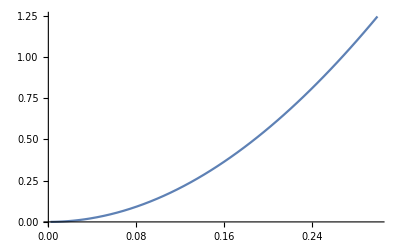

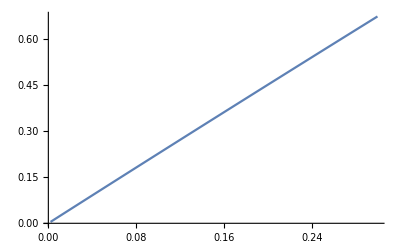

```mathematica
Plot[100*Cx/C0/.SolutionR1P2[[3,1]],{C0,0.002,0.3},PlotRange->All]
Plot[100*Cx/C0/.SolutionR1P1[[1,1]],{C0,0.002,0.3},PlotRange->All]
```